# Vacuum Stability

```mathematica
ClearAll["Global`*"];
```

```mathematica
SMparam={g-> 0.65,gY-> 0.36,yt-> 0.9945,mh-> 125.,v-> 174.,Q-> 150};
```

```mathematica
V0[λ_,A_,μH_,μS_,h_,S_]:=1/4 λ h^4-1/2 μH^2 h^2+1/2 μS^2 S^2-1/2 A S (h^2-2 v^2);
mW[h_]:=1/4 g^2 h^2;
mZ[h_]:=1/4(g^2+gY^2)h^2;
mt[h_]:=1/2 yt^2 h^2;
VCW[λ_,A_,μH_,μS_,h_]:=1/(64 π^2)(6 mW[h]^2(Log[mW[h]/Q^2]-5/6)+3 mZ[h]^2(Log[mZ[h]/Q^2]-5/6)-12 mt[h]^2(Log[mt[h]/Q^2]-3/2));
V0Tpre[λ_,A_,μH_,μS_,h_,S_]:=V0[λ,A,μH,μS,h,S]+VCW[λ,A,μH,μS,h];
```

```mathematica
μH‵renorm‵cond=μH/.Solve[(D[V0Tpre[λ,A,μH,μS,h,S],h]/.{h->√2 v,S->0})==0,μH]⟦2⟧
```

1/(8 √2)(√(-(3 g^4 v^2)/π^2-(2 g^2 gY^2 v^2)/π^2-(gY^4 v^2)/π^2+(48 v^2 yt^4)/π^2+256 v^2 λ+(6 g^4 v^2 Log[(g^2 v^2)/(2 Q^2)])/π^2+(3 g^4 v^2 Log[((g^2+gY^2) v^2)/(2 Q^2)])/π^2+(6 g^2 gY^2 v^2 Log[((g^2+gY^2) v^2)/(2 Q^2)])/π^2+(3 gY^4 v^2 Log[((g^2+gY^2) v^2)/(2 Q^2)])/π^2-(48 v^2 yt^4 Log[(v^2 yt^2)/Q^2])/π^2))

```mathematica
V0Tvac=V0Tpre[λ,A,μH‵renorm‵cond,μS,h,S]
```

-1/2 A S (h^2-2 v^2)+(h^4 λ)/4+(S^2 μS^2)/2+1/(64 π^2)(3/8 g^4 h^4 (-5/6+Log[(g^2 h^2)/(4 Q^2)])+3/16 (g^2+gY^2)^2 h^4 (-5/6+Log[((g^2+gY^2) h^2)/(4 Q^2)])-3 h^4 yt^4 (-3/2+Log[(h^2 yt^2)/(2 Q^2)]))-1/256 h^2 (-(3 g^4 v^2)/π^2-(2 g^2 gY^2 v^2)/π^2-(gY^4 v^2)/π^2+(48 v^2 yt^4)/π^2+256 v^2 λ+(6 g^4 v^2 Log[(g^2 v^2)/(2 Q^2)])/π^2+(3 g^4 v^2 Log[((g^2+gY^2) v^2)/(2 Q^2)])/π^2+(6 g^2 gY^2 v^2 Log[((g^2+gY^2) v^2)/(2 Q^2)])/π^2+(3 gY^4 v^2 Log[((g^2+gY^2) v^2)/(2 Q^2)])/π^2-(48 v^2 yt^4 Log[(v^2 yt^2)/Q^2])/π^2)

```mathematica
MassMatrix=D[V0Tvac,{{h,S},2}]/.{h->√2 v,S->0}/.SMparam//N//Simplify;
MassMatrix//MatrixForm
mh‵renorm=Eigensystem[MassMatrix]⟦1,2⟧
mS‵renorm=Eigensystem[MassMatrix]⟦1,1⟧
sinθ‵renorm=Eigensystem[MassMatrix]⟦2,1,1⟧
```

(-687.752+121104. λ | -246.073 A
-246.073 A | μS^2)

0.5 (-687.752+121104. λ+1. μS^2+1. √(473002.+242208. A^2-1.66579×10^8 λ+1.46662×10^10 λ^2+1375.5 μS^2-242208. λ μS^2+1. μS^4))

-0.5 (687.752-121104. λ-1. μS^2+1. √(473002.+242208. A^2-1.66579×10^8 λ+1.46662×10^10 λ^2+1375.5 μS^2-242208. λ μS^2+1. μS^4))

1/A 0.00203192 (687.752-121104. λ+1. μS^2+1. √(473002.+242208. A^2-1.66579×10^8 λ+1.46662×10^10 λ^2+1375.5 μS^2-242208. λ μS^2+1. μS^4))

```mathematica
{λ‵renorm,μS‵renorm,A‵renorm}={λ,μS,A}/.FindRoot[{mh‵renorm==125^2,mS‵renorm==5^2,sinθ‵renorm==0.17},{λ,0.13},{μS,5},{A,1}]
```

{0.131082,21.5215,10.4746}

```mathematica
μH‵renorm=μH‵renorm‵cond/.SMparam/.{λ->λ‵renorm}
```

93.1186

```mathematica
V0T[h_,S_]=V0Tpre[λ‵renorm,A‵renorm,μH‵renorm,μS‵renorm,h,S]/.SMparam
```

-4335.54 h^2+0.0327705 h^4-5.23728 (-60552.+h^2) S+231.588 S^2+1/(64 π^2)(0.0669398 h^4 (-5/6+Log[4.69444×10^-6 h^2])+0.0571527 h^4 (-5/6+Log[6.13444×10^-6 h^2])-2.93454 h^4 (-3/2+Log[0.0000219785 h^2]))

```mathematica
Plot3D[{V0T[h,S]},{h,0,5000},{S,0,100000}]
```

-Graphics3D-

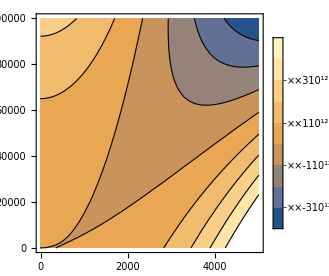

```mathematica
ContourPlot[V0T[h,S],{h,0,5000},{S,0,100000},PlotLegends->Automatic]
```

```mathematica
{hvev,Svev}={h,S}/.FindRoot[D[V0T[h,S],h]==0&&D[V0T[h,S],S]==0,{h,246},{S,0}]
```

{246.073,-1.70675×10^-12}

```mathematica
V0T[h,S]
```

-4335.54 h^2+0.0327705 h^4-5.23728 (-60552.+h^2) S+231.588 S^2+1/(64 π^2)(0.0669398 h^4 (-5/6+Log[4.69444×10^-6 h^2])+0.0571527 h^4 (-5/6+Log[6.13444×10^-6 h^2])-2.93454 h^4 (-3/2+Log[0.0000219785 h^2]))

```mathematica
FindMinimum[V0T[h,S],{{h,246},{S,0}}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-1.23106×10^8,{h→246.073,S→1.96723×10^-8}}

```mathematica
M=D[V0T[h,S],{{h,S},2}]/.{h->hvev,S->Svev}//Simplify
```

{{15186.8,-2577.51},{-2577.51,463.177}}

```mathematica
Sqrt[Eigenvalues[M]]
```

{125.,5.}

```mathematica
V0T[1000,10000]
```

-4.83055×10^9

```mathematica
Svevpath[h_]:=A/μS^2(h^2-hvev^2)/.{A->A‵renorm,μS->μS‵renorm}
```

```mathematica
Svevpath[1000]
```

21245.3

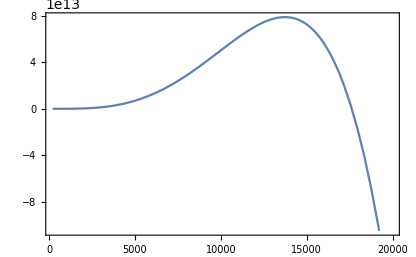

```mathematica
Plot[V0T[h,Svevpath[h]],{h,200,20000}]
```

```mathematica
Svevpath[15000]
```

5.08692×10^6

## Export

```mathematica
BP1‵V0T[h_,S_]=V0T;
DumpSave[NotebookDirectory[]<>"output/V0T_BP1.m",BP1‵V0T]
```

{BP1‵V0T}

## Check the bounce solution from simplebounce code

### Unit 100 GeV

```mathematica
pathdata=Drop[Import[NotebookDirectory[]<>"output/benchmark.csv","Data"][[2;;]],2];
Spath[h_]:=Interpolation[pathdata[[All,{2,3}]]][h];
hevolve[r_]:=Interpolation[pathdata[[All,{1,2}]]][r];
Sevolve[r_]:=Interpolation[pathdata[[All,{1,3}]]][r];
hpath[S_]:=Interpolation[pathdata[[All,{3,2}]]][S];
```

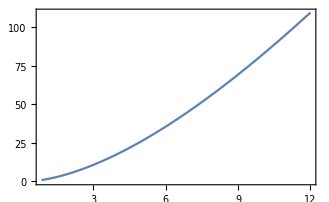

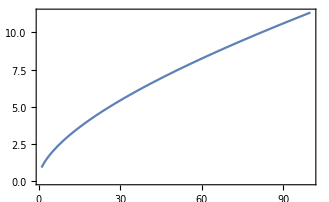

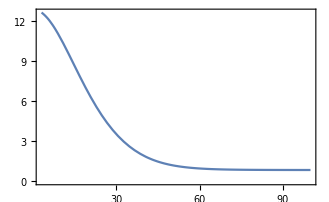

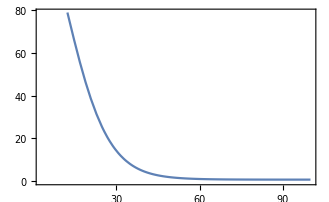

```mathematica
Plot[Spath[h],{h,.86,12.00}]
Plot[hpath[S],{S,1.00,100.00}]
Plot[hevolve[r],{r,3,100}]
Plot[Sevolve[r],{r,3,100}]
```

```mathematica
dV0Tdh[h_,S_]:=D[V0T[0.125299,10.6204,20.2598,21.8138,ϕ,S],{ϕ}]/.{ϕ->h};
dV0TdS[h_,S_]:=D[V0[0.125299,10.6204,20.2598,21.8138,h,ϕ],{ϕ}]/.{ϕ->S};
```

```mathematica
eqh[r_]:=hevolve''[r]+3/r hevolve'[r]-dV0Tdh[hevolve[r],Spath[hevolve[r]]];
eqs[r_]:=Sevolve''[r]+3/r Sevolve'[r]-dV0TdS[hpath[Sevolve[r]],Sevolve[r]];
```

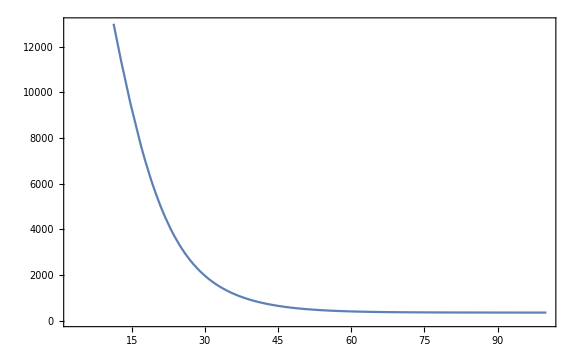

```mathematica
Plot[eqh[r],{r,3,100}]
```

```mathematica
eqh[80]
```

361.398

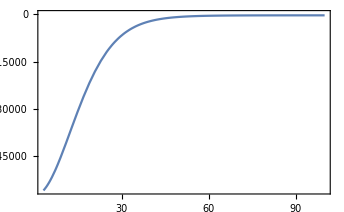

```mathematica
Plot[eqs[r],{r,3,100}]
```

### Unit GeV

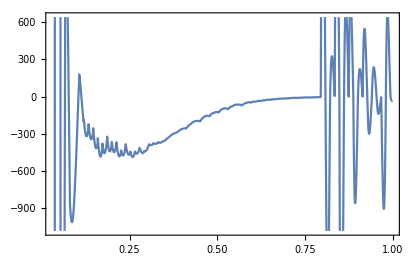

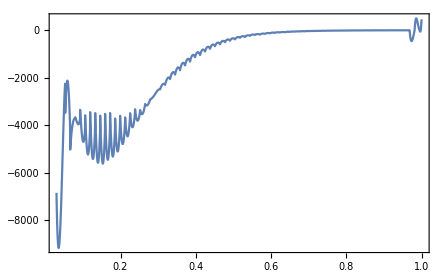

```mathematica
pathdata={0.01*#1,100*#2,100*#3}& @@@Drop[Import[NotebookDirectory[]<>"output/benchmark.csv","Data"][[2;;]],2];
Spath[h_]:=Interpolation[pathdata[[All,{2,3}]]][h];
hevolve[r_]:=Interpolation[pathdata[[All,{1,2}]]][r];
Sevolve[r_]:=Interpolation[pathdata[[All,{1,3}]]][r];
hpath[S_]:=Interpolation[pathdata[[All,{3,2}]]][S];
dV0Tdh[h_,S_]:=D[V0T[0.125299,10.6204,20.2598,21.8138,ϕ,S],{ϕ}]/.{ϕ->h};
dV0TdS[h_,S_]:=D[V0[0.125299,10.6204,20.2598,21.8138,h,ϕ],{ϕ}]/.{ϕ->S};
eqh[r_]:=hevolve''[r]+3/r hevolve'[r]-dV0Tdh[hevolve[r],Spath[hevolve[r]]];
eqs[r_]:=Sevolve''[r]+3/r Sevolve'[r]-dV0TdS[hpath[Sevolve[r]],Sevolve[r]];
Plot[eqh[r],{r,.03,1}]
Plot[eqs[r],{r,.03,1}]
```